# SystemStatistics package

## by Ian Hinder

## Initialisation

```mathematica
<<"SystemStatistics.m"
```

## Documentation

The SystemStatistics package contains functions for analysing performance and system statistics for simulations.

## Examples

```mathematica
run="D6q1_1a";
```

### Speed in physical time per hour

```mathematica
speed=ReadRunSpeed[run]
```

DataTable[...]

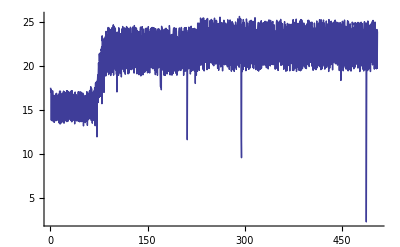

```mathematica
ListLinePlot[speed,PlotRange->{0,All}]
```

### Number of seconds of walltime for all segments

```mathematica
ReadWalltime[run]
```

85539.3

### Number of cores used

```mathematica
ReadCores[run]
```

64

### Maximum memory usage over all processes

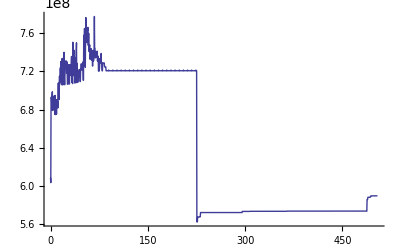

```mathematica
ListLinePlot[{ReadMemory[run]},PlotRange->{0,All}]
```

```mathematica
ListLinePlot[{ReadSwap[run]},PlotRange->{0,All}]
```

Throw::nocatch: Uncaught Cannot find file systemstatistics::process_memory_mb.maximum.asc in run D6q1_1a returned to top level.

Hold[Throw[Cannot find file systemstatistics::process_memory_mb.maximum.asc in run D6q1_1a]]

(The example simulation needs to be re-run with a more up-to-date version of SystemStatistics)

### CPU hours (core-hours)

```mathematica
ReadCPUHours[run]
```

1520.7